```mathematica
(* Set machine precision at start *)
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`400."&);
(* Matlab style linspace and logspace *)
linspace[start_,stop_,n_:100]:=start + (stop-start)*Subdivide[n-1];
linspace[start_,stop_,1]:=stop;
logspace[start_,stop_,n_:100]:=10.0^linspace[start,stop,n];
```

## Double precision

## Limit on summations for given λ

#### Summation terms for small values of λ : λ≤ 14

Define the vector containing the rate parameter λ. Note that we use direct summation primarily when λ≤ 13.5.

```mathematica
numM = 40;
Λ = N[logspace[-2,Log10[14],numM]];
```

Now the maximum number of summations follows from the observation that if u=1-2^-53 we need to do the most summations (when u=1 we simply have x=∞) and actually might have to use the top-down summation (if u>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again follows from the following:
We (roughly) stop the upward sum when x satisfies δ^*(1-u)=Prob(x,λ)/Prob(F^-1(u,λ)) so we find the maximal x by solving for x the equation 10^-17·2^-53=Prob(x,λ)/Prob(F^-1(1-2^-53,λ)) for various M.

```mathematica
Xtopdown = Table[If[Exp[-λ]>10^-17*2^-53,x/.FindRoot[SetPrecision[PDF[PoissonDistribution[λ],x]==10^-17*2^-53*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1-2^-53]],100],{x,0,Max[100,10*λ]},Method-> "Brent" , WorkingPrecision->100][[1]],0],{λ,Λ}];
```

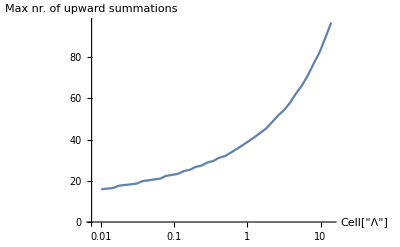

```mathematica
ListLogLinearPlot[TemporalData[Xtopdown,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"05dd0b7c-a6e3-47dc-a719-b50f73b25c4c"]","Max nr. of upward summations"}]
```

```mathematica
Ceiling[Xtopdown [[numM]] ]
```

97

Upper bound on the maximal number of iterations in the algorithm are therefore going to top-down summation while u=0.5 + ϵ . For that value of u the correct answer is roughly the mean λ and thus we must come down again to that value.

```mathematica
Ceiling[Xtopdown [[numM]] + (Xtopdown[[numM]]- Λ[[numM]])]
```

180

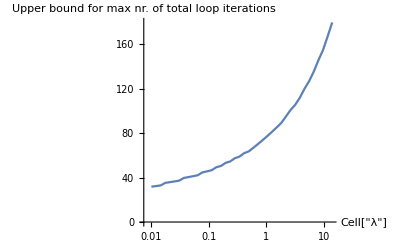

```mathematica
ListLogLinearPlot[TemporalData[2*Xtopdown-Λ,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["λ",ExpressionUUID->"1f167b45-d0f0-4b86-900f-9afb37e22c6c"]","Upper bound for max nr. of total loop iterations"}]
```

This is, however, a crude upper bound as when u=0.5 + ϵ we don’t sum all the way to the maximal x found earlier.

```mathematica
Xhigh = Table[If[Exp[-λ]>10^-17*2^-53,Floor[x/.FindRoot[SetPrecision[2*PDF[PoissonDistribution[λ],x]==10^-17*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1/2]],100],{x,0,Max[100,10*λ]},Method-> "Brent",WorkingPrecision->100][[1]]],0],{λ,Λ}];
```

```mathematica
2*Ceiling[Xtopdown[[numM]]] - Xhigh[[numM]]
```

136

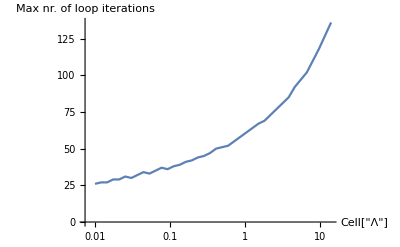

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[Xtopdown] - Xhigh,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"9fc3ec5f-26cf-4fe4-9d86-44ca540a052f"]","Max nr. of loop iterations"}]
```

#### Summation terms for larger values λ: λ>14 and u≤ F(10,λ)

Now note that when λ>13.5 we only use the summation when u≤ F(10,λ). Note that for λ≥ 796.15 we have F(10,λ)< 2^-1074 and thus we will never use direct summation in that case. 
When 10.6685 <12< λ<796.15 we have 2^-1074≤ F(10,λ)<0.5 and therefore only use bottom-up summation, which has at most 10 iterations, as u≤ F(10,λ).

## Single precision

## Limit on summations for given λ

#### Summation terms for small values of λ : λ≤ 4

Define the vector containing the rate parameter λ. Note that we use direct summation primarily when λ≤ 4.

```mathematica
numM = 40;
Λ = N[logspace[-2,Log10[4],numM]];
```

Now the maximum number of summations follows from the observation that if u=1-2^-24 we need to do the most summations (when u=1 we simply have x=∞) and actually might have to use the top-down summation (if u>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again follows from the following:
We stop the upward sum when x satisfies δ^*(1-u)=Prob(x,λ)/Prob(F^-1(u,λ)) so we find the maximal x by solving for x the equation 10^-7·2^-24=Prob(x,λ)/Prob(F^-1(1-2^-24,λ)) for various M.

```mathematica
Xtopdown = Table[If[Exp[-λ]>10^-7*2^-24,x/.FindRoot[SetPrecision[PDF[PoissonDistribution[λ],x]==10^-7*2^-24*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1-2^-24]],100],{x,0,Max[100,10*λ]},Method-> "Brent" , WorkingPrecision->100][[1]],0],{λ,Λ}];
```

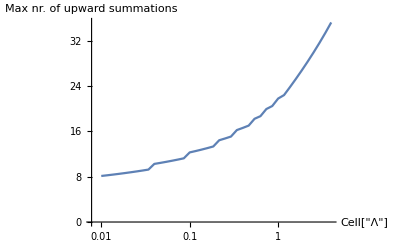

```mathematica
ListLogLinearPlot[TemporalData[Xtopdown,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"a9753d65-39cc-4df5-87a2-9d5a1ab1efd0"]","Max nr. of upward summations"}]
```

```mathematica
Ceiling[Xtopdown [[numM]] ]
```

36

Upper bound on the maximal number of iterations in the algorithm are therefore going to top-down summation while u=0.5 + ϵ . For that value of u the correct answer is roughly the mean λ and thus we must come down again to that value.

```mathematica
Ceiling[Xtopdown [[numM]] + (Xtopdown[[numM]]- Λ[[numM]])]
```

67

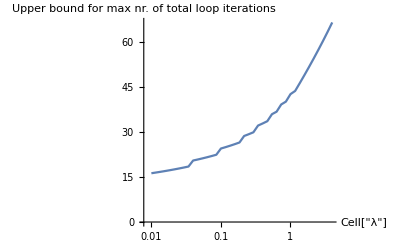

```mathematica
ListLogLinearPlot[TemporalData[2*Xtopdown-Λ,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["λ",ExpressionUUID->"9a10b355-9cd3-4afa-a7c1-5438b3853808"]","Upper bound for max nr. of total loop iterations"}]
```

This is, however, a crude upper bound as when u=0.5 + ϵ we don’t sum all the way to the maximal x found earlier.

```mathematica
Xhigh = Table[If[Exp[-λ]>10^-7*2^-24,Floor[x/.FindRoot[SetPrecision[2*PDF[PoissonDistribution[λ],x]==10^-7*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1/2]],100],{x,0,Max[100,10*λ]},Method-> "Brent",WorkingPrecision->100][[1]]],0],{λ,Λ}];
```

```mathematica
2*Ceiling[Xtopdown[[numM]]] - Xhigh[[numM]]
```

53

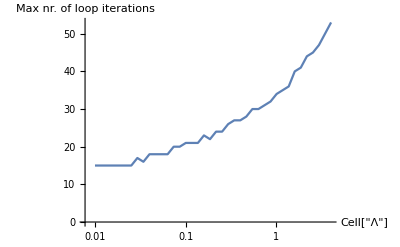

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[Xtopdown] - Xhigh,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"7d180eda-d99e-4e78-a31f-1d79421cb951"]","Max nr. of loop iterations"}]
```

#### Summation terms for larger values of λ: λ>4 and u≤ F(10,λ)

Now note that when λ>4 we only use the summation when u≤ F(10,λ). Note that for λ≥ 134.6712 we have F(10,λ)< 2^-149 and thus we will never use direct summation in that case. 
When 10.6685 < λ<134.6712 we have 2^-149≤ F(10,λ)<0.5 and therefore only use bottom-up summation, which has at most 10 iterations, as u≤ F(10,λ).
When 4<λ≤ 10.6685 we have F(10,λ)≥ 0.5 and thus we could be having to use top-down summation. And we do a final check to see how many summations this could result in, similarly to before:

```mathematica
numM = 40;
Λ = N[logspace[Log10[4],Log10[10.7],numM]];
```

```mathematica
Xtopdown = Table[If[Exp[-λ]>10^-7*2^-24,x/.FindRoot[SetPrecision[PDF[PoissonDistribution[λ],x]==10^-7*2^-24*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1-2^-24]],100],{x,0,Max[100,10*λ]},Method-> "Brent" , WorkingPrecision->100][[1]],0],{λ,Λ}];
```

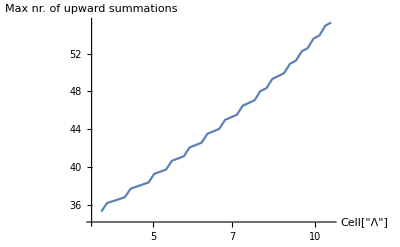

```mathematica
ListLogLinearPlot[TemporalData[Xtopdown,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"7d77371e-8a15-4713-85c1-98cec5b7a257"]","Max nr. of upward summations"}]
```

```mathematica
Ceiling[Max[Xtopdown]]
```

56

```mathematica
Xhigh = Table[If[Exp[-λ]>10^-7*2^-24,Floor[x/.FindRoot[SetPrecision[2*PDF[PoissonDistribution[λ],x]==10^-7*PDF[PoissonDistribution[λ],InverseCDF[PoissonDistribution[λ],1/2]],100],{x,0,Max[100,10*λ]},Method-> "Brent",WorkingPrecision->100][[1]]],0],{λ,Λ}];
```

```mathematica
2*Ceiling[Xtopdown[[numM]]] - Xhigh[[numM]]
```

78

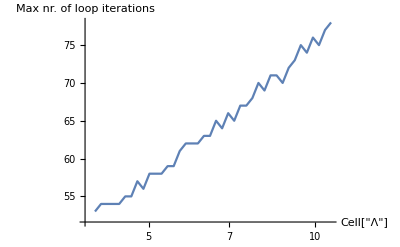

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[Xtopdown] - Xhigh,{Λ}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["Λ",ExpressionUUID->"4cf65f45-b98e-4e1d-a231-9f45183a269e"]","Max nr. of loop iterations"}]
```